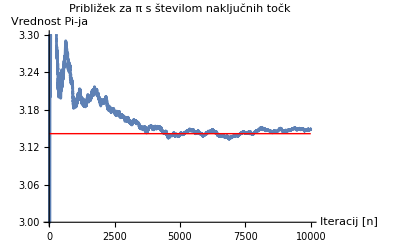

Približek za π:3.13241

Relativna napaka:0.00292146

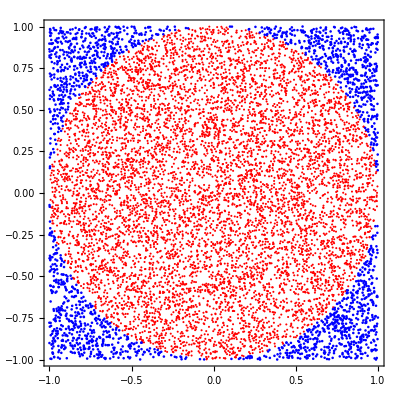

```mathematica
Get["C:\\Users\\jurek\\OneDrive\\Namizje\\3. Letnik\\NROR\\2. domaca naloga\\mccpi.nb"
];

(*Določimo Število naključnih točk*)
n=10000;
VariacijaPi[n]



VariacijaPi[n_]:=Module[
(*Za variacijo pi-ja z večanjem naključnih števil*)
{count,x,y,notr,pi1,tocnPi},

count=0;
notr=0;
pi1={};
tocnPi=N[Pi];

SeedRandom[123];

For[i=1,i<=n,i++,x=RandomReal[1];
y=RandomReal[1];
If[x^2+y^2<=1,notr++];
count++;
AppendTo[pi1,4 notr/count];];



ListLinePlot[pi1,PlotRange->{3,3.3},AxesLabel->{"Iteracij [n]","Vrednost Pi-ja"},PlotLabel->"Približek za π s številom naključnih točk",Epilog->{Red,Line[{{0,tocnPi},{n,tocnPi}}]}]]

Clear[tockenotr,tockezuni,naspi,napaka,tocnipi]
tockenotr=mccpi[n][[1]];
tockezuni=mccpi[n][[2]];
tocnipi=N[Pi];
naspi=4 Length[tockenotr]/(Length[tockenotr]+Length[tockezuni]);
napaka=Abs[naspi-tocnipi]/tocnipi;
(*Izpis Napake in vrednosti Pi-ja*)
Print["Približek za π:",N[naspi]];
Print["Relativna napaka:",N[napaka]];
(*Prikaz grafa naključnih točk*)
Show[
ListPlot[tockenotr,PlotStyle->{Red},PlotStyle->PointSize[0.02],AspectRatio->1,Frame->True,Axes->False],
ListPlot[tockezuni,PlotStyle->{Blue},PlotStyle->PointSize[0.02],AspectRatio->1,Frame->True,Axes->False]
]
```